BLACKBODY RADIATION

Radiation

All bodies emit and absorb electromagnetic radiation. When a body and its surrounding have the same temperature, the amount of radiation emitted  is equal to the amount of radiation absorbed. The power of body’s radiation is proportional to its surface area and to the fourth power of its absolute temperature. Josef Stefan observed this result in the year 1879 but it was Ludwig Boltzmann who derived this finding theoretically after five years. This result is now called Stefan-Boltzmann law:

P_r=eσAT^4 where

P_r=power radiated

A=surface area

σ = universal constant = 5.6703×10^-8 W/(m^2·K^4)

e = emissivity of the radiating surface. It is unitless constant between 0 and 1 that depends on surface properties of the body

Part of electromagnetic radiation on a body is reflected and the other part is absorbed but dark body absorbs most of the radiation.

If the body has temperature T_0 it absorbs radiation at a rate given by

P_a=eσAT_o^4

If the body at temperature T and the objects at its surrounding have temperature T_o the net power of radiation coming the body is

P_net= eσA(T^4-T_o^4)

If the body emits more radiant energy it becomes cooler but if the surrounding emits more radiant energy the body absorbs radiation and becomes warmer.

If the body and the surrounding have the same temperature then the body emits and absorbs radiation equally.

A blackbody ( or an ideal radiator) is a body that absorbs all radiation on it with emissivity equal to 1.

It is possible to calculate theoretically the characteristics of the radiation.

Between 600 °C and 700°C the radiant energy of the object becomes visible as shown in its lightly reddening surface.

As the temperature increases the surface of the object becomes brightly red, orange , or even yellow at higher temperature.

THe figure below shows the blackbody power as a function of wavelengths of three different temperatures.

-Graphics-

The wavelength is inversely proportional to the Kelvin temperature at which the power is maximum. This law is also know as Wein’s displacement law:

λ_max = (2.898 mm·K)/T

The surface temperature of the stars can be determined using this law.  The temperatures in the different regions of the surface of the object can be mapped out using Wien’s displacement law.

A thermograph is a device that continuously records temperature changes over time.

In medical thermography a thermograph is used to detect heat patterns, specially the cancerous skin, in the human body.

-Graphics-

Classical thermodynamics calculated theoretically the blackbody spectral distributions but  Max Planck quantized the energy  which resolved the discrepancy with the Rayleigh-Jeans law that has an ultraviolet catastrophe.

Sample problem  The maximum power of radiation emitted by the Sun surface  has approximately a wavelength of 500 nm. (a) What is the surface temperature of the Sun considering that it is a blackbody emitter? (b) Find the wavelength λ_max of a blackbody at 100°C. (c) Compare both wavelengths. Compare also their temperatures.

SOLUTION

(a) We use the Wien’s law λ_max=(2.898mm·K)/T->T=(2.989 mm·K)/(500 nm) ≈ 5800 K

(b) λ_max= (2.898 mm·K)/((100+273.15) K) = 0.000007766 ≈7.77×10^-6=7.77 μ m.

(c) 0.000007766/500 nm ≈ 16. The wavelength at 100°C is almost 16 times greater than the wavelength near the surface of the Sun.

Also their temperatures comparison is 5800 K/373.15 K ≈16 . The temperature at the sun surface is 16 times greater than the temperature of the blackbody at 100°C.

The Sun maximum wavelength is visible in the spectrum so the Sun’s radiation spectrum is fair.

The infrared maximum wavelength is longer than the wavelength visible to the eyes.

The human skins although they are not black to our eyes can be considered as blackbodies for  absorption and emission so the emissivity of the skin 1.0.

RADIATION FROM HUMAN BODY

Problem: Suppose a naked person as a blackbody has a total surface area of 1.3 m^2 inside a room where the temperature is 22°C.  If the temperature of the person is 34°C, find the rate of heat loss that radiates from the person.

SOLUTION

Substitue T_0=(22+273.15)K = 295.15 K, T = (34 + 273.15) K = 307.15 K, Stefan constant σ= 5.6703×10^-8 W/(m^2·K^4), and e=1 in

P_net=eσA(T^4-T_0^4)= 96.67 ≈ 97 W.

By wearing clothing with low thermal conductivity we protect our selves from this loss of heat.

If the temperature T of the object is approximate equal to the  temperature T_0 of the surroundings then

P_net=eσA(T^4-T_0^4)=eσA (T^2+T_0^2) (T^2-T_0^2). By replacing T with T_0 we have

eσA (T_0^2+T_0^2) (T_0+T_0)(T-T_0) = 4 eσAT_0^3ΔT or we have

ΔP_r≈ dP_r/dT|_(T=T_0) (T - T_0) = 4 eσAT_0^3ΔT

------------------------------------------------------------------------------------------------------------------------------------

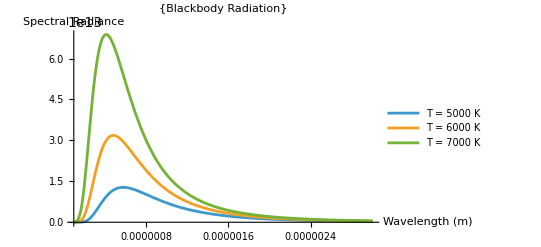

```mathematica
h=6.626*10^-34;
c=300000000;
k=1.381*10^-23;
Plot[{(2*h*c^2)/(λ^5*(Exp[(h*c)/(λ*k*5000)]-1)),(2*h*c^2)/(λ^5*(Exp[(h*c)/(λ*k*6000)]-1)),(2*h*c^2)/(λ^5*(Exp[(h*c)/(λ*k*7000)]-1))},{λ,100*10^-9,3000*10^-9},PlotRange->All,ImageSize->{600},PlotLabel->{"Blackbody Radiation"},PlotLegends->{"T = 5000 K","T = 6000 K","T = 7000 K"},AxesLabel->{"Wavelength (m)","Spectral Radiance"}]
```

PLANCK’S LAW

-Graphics-

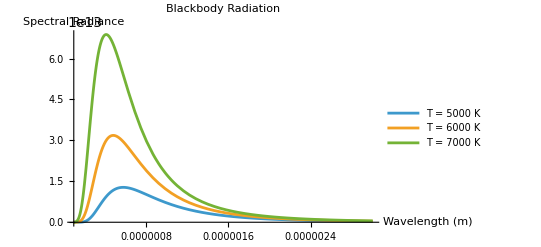

```mathematica
h=6.626*10^-34;
c=3*10^8;
kB=1.381*10^-23;

planck[λ_,T_]:=(2 h c^2)/(λ^5 (Exp[(h c)/(λ kB T)]-1));

Plot[{planck[λ,5000],planck[λ,6000],planck[λ,7000]},{λ,100*10^-9,3000*10^-9},PlotRange->All,AxesLabel->{"Wavelength (m)","Spectral Radiance"},PlotLegends->{"T = 5000 K","T = 6000 K","T = 7000 K"},PlotLabel->"Blackbody Radiation",ImageSize->{500}]
```

Rayleigh-Jeans law

```mathematica
c=300000000;
k=1.381*10^-23;
```

```mathematica
Plot[(2*c*k*5000)/λ^4,{λ,100*10^-9,3000*10^-9},PlotRange->All,PlotLabel->"Rayleigh–Jeans Law",AxesLabel->{"Wavelength (m)","Spectral Radiance (W/m.b3)"},ImageSize->{500}]
```

-Graphics-

```mathematica
(*Define physical constants in SI units*)c=Quantity["SpeedOfLight"]//UnitConvert//QuantityMagnitude;
kB=Quantity["BoltzmannConstant"]//UnitConvert//QuantityMagnitude;

(*Define the Rayleigh–Jeans law function for spectral radiance*)
rayleighJeans[λ_,T_]:=(2*c*kB*T)/λ^4;

(*Choose a temperature,e.g.,5000 Kelvin*)
T0=5000;

(*Plot the Rayleigh–Jeans spectral radiance for wavelengths from 100 nm to 3000 nm*)
Plot[rayleighJeans[λ,T0],{λ,100*10^-9,3000*10^-9},AxesLabel->{"Wavelength (m)","Spectral Radiance (W/m.b3)"},PlotLabel->"Rayleigh–Jeans Law at "<>ToString[T0]<>" K",PlotRange->All, ImageSize->{500}]
```

-Graphics-

c = Quantity[“SpeedOfLight”] // UnitConvert // QuantityMagnitude // N
kB = Quantity[“BoltzmannConstant”] // UnitConvert // QuantityMagnitude // N

```mathematica
c=Quantity["SpeedOfLight"]//UnitConvert//QuantityMagnitude//N
kB=Quantity["BoltzmannConstant"]//UnitConvert//QuantityMagnitude//N
```

2.99792×10^8

1.38065×10^-23

DIFFERENCE BETWEEN RAYLEIGH-JEANS LAW AND PLANCK’S LAW

The Rayleigh-Jeans Law and Planck’s Law both describe the spectral radiance of blackbody radiation, but they differ in their assumptions and accuracy at different wavelengths.

Rayleigh-Jeans Law is a classical approximation for blackbody radiation, given by:

B_λ(λ,T)=(2 ck_B T)/λ^4 where

B_λ is the spectral radiance,

c is the speed of light,

k_B is Boltzmann's constant,

T is the temperature in Kelvin,

λ is the wavelength

Valid at long wavelength (low frequencies).

Fails at short wavelengths (high frequencies), leading to the ultraviolet catastrophe, where the predicted energy diverges to infinity.

Planck’s law

Planck’s law correctly describes blackbody radiation by incorporating quantum mechanics

B_λ(λ,T)=(2 hc^2)/(λ^5(e^(hc/(λk_B T))-1)) where

h is the Planck's constant equal to 6.626×10^-34 J·s,

Accurate at all wavelengths, solving the ultraviolet catastrophe

Reduces to the Rayleigh-Jeans law at long wavelengths ( when wavelength is  large, e^(hc/(λk_B T))≈ 1 + hc/(λk_B T), leading to the classical result).

Reduces to Wien’sLaw at short wavelengths (where only high-energy photons contribute).

Key Difference

```mathematica
Grid[{{"Feature","Rayleigh-Jeans Law","Planck’s Law"},{"Based on","Classical physics","Quantum Mechanics"},{"Validity Range","Long wavelengths (low frequency)","All wavelengths"},{"Ultraviolet Catastrophe","Yes (diverges at short wavelengths)","No (finite energy at all wavelengths)"},{"Derived from","Equipartition Theorem","Photon energy quantization"}},Frame->All,Background->{{1->LightGray},None}]
```

Feature | Rayleigh-Jeans Law | Planck’s Law
Based on | Classical physics | Quantum Mechanics
Validity Range | Long wavelengths (low frequency) | All wavelengths
Ultraviolet Catastrophe | Yes (diverges at short wavelengths) | No (finite energy at all wavelengths)
Derived from | Equipartition Theorem | Photon energy quantization

```mathematica
(* Key Differences *)
```

Feature | Rayleigh-Jeans Law | Planck’s Law
Based on | Classical physics | Quantum Mechanics
Validity Range | Long wavelengths (low frequency) | All wavelengths
Ultraviolet Catastrophe | Yes (diverges at short wavelengths) | No (finite energy at all wavelengths)
Derived from | Equipartition Theorem | Photon energy quantization

Planck’s law corrected the flaws of the Rayleigh-Jeans law and led to the development of quantum mechanics.

```mathematica
Series[E^x,{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

EQUIPARTION THEOREM

The equipartition theorem states that, in thermal equilibrium, each quadratic degree of freedom of a system contributes an average energy of 1/2 k_B T, where k_B is the Boltzmann constant (1.38×10^-23 J/K) and T is the absolute temperature in Kelvin.

Example: Energy of a Monatomic gas (Ideal Gas)

A monatomic gas (e.g., helium, neon) has 3 translational degrees of freedom (motion in x, y, and z directions). According to the equipartition theorem, the average kinetic energy per molecule is

E_avg=3/2 k_B T

Let’s calculate this at T= 300 K (room temperature);

E_avg=3/2(1.38×10^-23)×300 = 6.21×10^-21 J

Total energy of 1 Mole of Gas

For 1 mole of gas, multiply by Avogadro’s number N_A=6.022×10^-23:

E_total=(6.21×10^-21)×(6.21×10^23)=3.74 kJ

Thus, at 300 K, one mole of a monatomic gas has 3.74 kJ of internal energy due to translational motion.

Let’s extend the equipartition theorem to diatomic and polyatomic gases.

1. Diatomic Gas (e.g., O_2,N_2)

A diatomic gas has 5 degrees of freedom at room temperature:

3 translational (motion in x,y,z directions).

2 rotational (rotation about two perpendicular axes; the third axis along the bond axis is negligible at low temperatures).

Thus, the average energy per molecule:

E_avg=5/2 k_B T

At T =300 K, using 1.38×10^-23 J/K:

E_avg=5/2×(1.38×10^-23)×300 = 1.035×10^-23 J.

For one mole of a diatomic gas:

E_total=(1.035×10^-23)×6.022×10^23 = 6.23 kJ

Thus, at 300 K, one mole of a diatomic gas has 6.23 kJ of internal energy due to translation and rotation.

2. Polyatomic Gas (e.g., CO_2,CH_4)

A nonlinear polyatomic gas (e.g., methane, carbon dioxide) has 6 degrees at room temperature:

3 translation

3 rotational (since nonlinear molecules can rotate around all three perpendicular axes)

So, the average energy per molecule:

E_avg=6/2 k_B T=3 k_B T

At T = 300 K: E_avg=6/2 k_B T=3(1.38×10^-23)^-20×300 = 1.24×10^-20 J

For a mole of a polyatomic gas:

E_total=(1.24×10^-24)×(6.022×10^23) = 7.46 kJ

Thus, at 300 K, one mole of a nonlinear polyatomic gas has 7.46 kJ of internal energy.

Summary Table at 300 K

```mathematica
Grid[{{"Gas Type","Degrees of Freedom","Energy per Molecule","Energy per Mole (kJ)"},{"Monatomic (He, Ne)","3","6.21×10^-21","3.74"},{"Diatomic(O_2,N_2","5","1.035×10^-20","6.23"},{"Polytomic(CO_2,CH_4)","6","1.24×10^-20","7.46"}},Frame->All,Background->{{1->LightGray},None}]
```

Gas Type | Degrees of Freedom | Energy per Molecule | Energy per Mole (kJ)
Monatomic (He, Ne) | 3 | 6.21×10^-21 | 3.74
Diatomic(O_2,N_2 | 5 | 1.035×10^-20 | 6.23
Polytomic(CO_2,CH_4) | 6 | 1.24×10^-20 | 7.46